```mathematica
(* Computations for solving that appropriate α and γ to satisfy the conditions with β. *)
v=X1-X0;
tDDX0=-(√A0)/4(7 √A0+3 √B0);
tDDX1=(√B0)/4(3 √A0+7 √B0);
fDDX0=(ratio)DDX0+(1-ratio)tDDX0;
fDDX1=(ratio)DDX1+(1-ratio)tDDX1;
h=(U1-U0)/2;
A0=DX0*2*h/v;
B0=DX1*2*h/v;
C0=fDDX0*h*(h/v);
D0=fDDX1*h*(h/v);
a=B0;
b=4*(B0-D0);
c=30-6*(2*(A0+B0)+C0-D0);
d=4*(A0+C0);
e=A0;
alpha=b*a^(-3/4)*e^(-1/4);
beta=c*a^(-1/2)*e^(-1/2);
gamma=d*a^(-1/4)*e^(-3/4);
(* Simplify the expressions. Replace[<expression>,{(DX0 (U0-U1))/(X0-X1)->A0,(DX1 (U0-U1))/(X0-X1)->B0}] *)
alpha=Collect[Simplify[ExpandAll[alpha]],{ratio}]/.{(DX0 (U0-U1))/(X0-X1)->A,(DX1 (U0-U1))/(X0-X1)->B};
gamma=Collect[Simplify[ExpandAll[gamma]],{ratio}]/.{(DX0 (U0-U1))/(X0-X1)->A,(DX1 (U0-U1))/(X0-X1)->B};
beta=Collect[Simplify[ExpandAll[beta]],{ratio}]/.{(DX0 (U0-U1))/(X0-X1)->A,(DX1 (U0-U1))/(X0-X1)->B};
Print[]
Print["alpha = ",alpha]
Print["gamma = ",gamma]
Print["beta  = ",beta]
(* Get the coefficient lists in terms of ratio, rewrite in simple form. *)
acl=CoefficientList[alpha,ratio];
gcl=CoefficientList[gamma,ratio];
bcl=CoefficientList[beta,ratio];
alpha=ax(ratio)+ay;
gamma=gx(ratio)+gy;
beta=bx(ratio)+by;
Print[]
Print["----------------------------------------------------------------"]
Print[]
(* Compute all of the solutions to the problem. *)
(* CASE 1: (alpha == bound) AND (bound ≤ 6) *)
solution=Solve[{alpha==(-(beta+2)/2)},{ratio}];
sol1=solution[[1]][[1]][[2]];
(* CASE 2: (gamma == bound) AND (bound ≤ 6) *)
solution=Solve[{gamma==(-(beta+2)/2)},{ratio}];
sol2=solution[[1]][[1]][[2]];
(* CASE 3: (alpha == bound) AND (bound > 6) *)
solution=Solve[{alpha==(-2 √(beta-2))},{ratio}];
sol3a=solution[[1]][[1]][[2]];
sol3b=solution[[2]][[1]][[2]];
(* CASE 4: (gamma == bound) AND (bound > 6) *)
solution=Solve[{gamma==(-2 √(beta-2))},{ratio}];
sol4a=solution[[1]][[1]][[2]];
sol4b=solution[[2]][[1]][[2]];
(* ----------------------------------------------------------------------------- *)
ax=acl[[1]];
ay=acl[[2]];
gx=gcl[[1]];
gy=gcl[[2]];
bx=bcl[[1]];
by=bcl[[2]];
(* Print all of the solutions out in a readable form (that can be copied to code). *)
Print["Alpha equals bound for beta <= 6"]
Print["ratio = ",sol1//ExpandAll//Simplify//FortranForm]
Print[]

Print["Gamma equals bound for beta <= 6"]
Print["ratio = ",sol2//ExpandAll//Simplify//FortranForm]
Print[]


Print["Alpha equals bound for beta > 6"]
Print["ratio = ",sol3a//Simplify//FortranForm]
Print["ratio = ",sol3b//Simplify//FortranForm]
Print[]

Print["Gamma equals bound for beta > 6"]
Print["ratio = ",sol4a//Simplify//FortranForm]
Print["ratio = ",sol4b//Simplify//FortranForm]
Print[]
```

alpha = -(A^(3/4) ratio (7 DX1 U0^2-14 DX1 U0 U1+7 DX1 U1^2+3 √A √B (U0-U1) (X0-X1)-4 DDX1 (U0-U1) (X0-X1)))/(4 B^(3/4) DX0 (X0-X1))-(A^(3/4) (-7 DX1 U0^2+14 DX1 U0 U1-7 DX1 U1^2-3 √A √B (U0-U1) (X0-X1)+16 DX1 (-X0+X1)))/(4 B^(3/4) DX0 (X0-X1))

gamma = -(A^(1/4) ratio (7 DX0 U0^2-14 DX0 U0 U1+7 DX0 U1^2+3 √A √B (U0-U1) (X0-X1)+4 DDX0 (U0-U1) (X0-X1)))/(4 B^(1/4) DX0 (X0-X1))-(A^(1/4) (-7 DX0 U0^2+14 DX0 U0 U1-7 DX0 U1^2-3 √A √B (U0-U1) (X0-X1)+16 DX0 (-X0+X1)))/(4 B^(1/4) DX0 (X0-X1))

beta  = 1/(8 √A √B (X0-X1)^2)3 ratio (7 DX0 U0^2 (U0-U1)+7 DX1 U0^2 (U0-U1)-14 DX0 U0 (U0-U1) U1-14 DX1 U0 (U0-U1) U1+7 DX0 (U0-U1) U1^2+7 DX1 (U0-U1) U1^2+6 √A √B U0^2 (X0-X1)+4 DDX0 (U0-U1)^2 (X0-X1)-4 DDX1 (U0-U1)^2 (X0-X1)-12 √A √B U0 U1 (X0-X1)+6 √A √B U1^2 (X0-X1))+1/(8 √A √B (X0-X1)^2)3 (-7 DX0 U0^2 (U0-U1)-7 DX1 U0^2 (U0-U1)+14 DX0 U0 (U0-U1) U1+14 DX1 U0 (U0-U1) U1-7 DX0 (U0-U1) U1^2-7 DX1 (U0-U1) U1^2-6 √A √B U0^2 (X0-X1)+12 √A √B U0 U1 (X0-X1)-6 √A √B U1^2 (X0-X1)+80 X0 (X0-X1)-80 (X0-X1) X1+32 DX0 (U0-U1) (-X0+X1)+32 DX1 (U0-U1) (-X0+X1))

----------------------------------------------------------------

Alpha equals bound for beta <= 6

ratio = (3*B**0.25*DX0*(U0 - U1)**2*(7*DX0*(U0 - U1) + 7*DX1*(U0 - U1) + 4*(DDX0 - DDX1)*(X0 - X1)) + 2*Sqrt(A)*B**0.75*DX0*(9*U0**2 - 18*U0*U1 + 9*U1**2 + 8*X0 - 8*X1)*(X0 - X1) - 12*A**1.75*Sqrt(B)*(U0 - U1)*(X0 - X1)**2 - 4*A**1.25*(U0 - U1)*(X0 - X1)*(7*DX1*(U0 - U1) + 4*DDX1*(-X0 + X1)))/(3*B**0.25*DX0*(DX0*(U0 - U1)*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 32*X0 - 32*X1) + DX1*(U0 - U1)*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 32*X0 - 32*X1) - 80*(X0 - X1)**2) + 18*Sqrt(A)*B**0.75*DX0*(U0 - U1)**2*(X0 - X1) - 4*A**1.25*DX1*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 16*(X0 - X1))*(X0 - X1) - 12*A**1.75*Sqrt(B)*(U0 - U1)*(X0 - X1)**2)

Gamma equals bound for beta <= 6

ratio = (21*DX0**2*(U0 - U1)**3 + 21*DX0*DX1*(U0 - U1)**3 + 2*DX0*(-14*A**0.75*B**0.25*(U0 - U1)**2 + 6*(DDX0 - DDX1)*(U0 - U1)**2 + Sqrt(A)*Sqrt(B)*(9*U0**2 - 18*U0*U1 + 9*U1**2 + 8*X0 - 8*X1))*(X0 - X1) - 4*A**0.75*B**0.25*(3*Sqrt(A)*Sqrt(B) + 4*DDX0)*(U0 - U1)*(X0 - X1)**2)/(3*DX0**2*(U0 - U1)*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 32*(X0 - X1)) + 3*DX0*DX1*(U0 - U1)*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 32*(X0 - X1)) - 2*DX0*(-9*Sqrt(A)*Sqrt(B)*(U0 - U1)**2 + 2*A**0.75*B**0.25*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 16*X0 - 16*X1) + 120*(X0 - X1))*(X0 - X1) - 12*A**1.25*B**0.75*(U0 - U1)*(X0 - X1)**2)

Alpha equals bound for beta > 6

ratio = (B**1.5*DX0**2*(X0 - X1)**2*((A**1.5*(U0 - U1)*(7*DX1*(U0 - U1) + (3*Sqrt(A)*Sqrt(B) - 4*DDX1)*(X0 - X1))*(DX1*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 16*X0 - 16*X1) + 3*Sqrt(A)*Sqrt(B)*(U0 - U1)*(X0 - X1)))/(B**1.5*DX0**2*(X0 - X1)**2) - (12*(DX0*(U0 - U1)*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 32*(X0 - X1)) + DX1*(U0 - U1)*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 32*(X0 - X1)) + 2*(X0 - X1)*(3*Sqrt(A)*Sqrt(B)*(U0 - U1)**2 + 40*(-X0 + X1))))/(Sqrt(A)*Sqrt(B)*(X0 - X1)**2) - 2*Sqrt(2)*Sqrt((3*(U0 - U1)**2*(7*DX0*(U0 - U1) + 7*DX1*(U0 - U1) + 2*(3*Sqrt(A)*Sqrt(B) + 2*DDX0 - 2*DDX1)*(X0 - X1))*(A*DX1*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 16*X0 - 16*X1) + 3*A**1.5*Sqrt(B)*(U0 - U1)*(X0 - X1))**2 - 16*A**2.5*Sqrt(B)*(DX1*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 16*X0 - 16*X1) + 3*Sqrt(A)*Sqrt(B)*(U0 - U1)*(X0 - X1))**2*(X0 - X1)**2 - 3*A**2*(U0 - U1)*(7*DX1*(U0 - U1) + (3*Sqrt(A)*Sqrt(B) - 4*DDX1)*(X0 - X1))*(DX1*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 16*X0 - 16*X1) + 3*Sqrt(A)*Sqrt(B)*(U0 - U1)*(X0 - X1))*(DX0*(U0 - U1)*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 32*(X0 - X1)) + DX1*(U0 - U1)*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 32*(X0 - X1)) + 2*(X0 - X1)*(3*Sqrt(A)*Sqrt(B)*(U0 - U1)**2 + 40*(-X0 + X1))) + 18*B*DX0**2*(DX0*(U0 - U1)*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 32*(X0 - X1)) + DX1*(U0 - U1)*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 32*(X0 - X1)) + 2*(X0 - X1)*(3*Sqrt(A)*Sqrt(B)*(U0 - U1)**2 + 40*(-X0 + X1)))**2)/(A*B**2*DX0**2*(X0 - X1)**4))))/(A**1.5*(DX1*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 16*X0 - 16*X1) + 3*Sqrt(A)*Sqrt(B)*(U0 - U1)*(X0 - X1))**2)

ratio = (B**1.5*DX0**2*(X0 - X1)**2*((A**1.5*(U0 - U1)*(7*DX1*(U0 - U1) + (3*Sqrt(A)*Sqrt(B) - 4*DDX1)*(X0 - X1))*(DX1*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 16*X0 - 16*X1) + 3*Sqrt(A)*Sqrt(B)*(U0 - U1)*(X0 - X1)))/(B**1.5*DX0**2*(X0 - X1)**2) - (12*(DX0*(U0 - U1)*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 32*(X0 - X1)) + DX1*(U0 - U1)*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 32*(X0 - X1)) + 2*(X0 - X1)*(3*Sqrt(A)*Sqrt(B)*(U0 - U1)**2 + 40*(-X0 + X1))))/(Sqrt(A)*Sqrt(B)*(X0 - X1)**2) + 2*Sqrt(2)*Sqrt((3*(U0 - U1)**2*(7*DX0*(U0 - U1) + 7*DX1*(U0 - U1) + 2*(3*Sqrt(A)*Sqrt(B) + 2*DDX0 - 2*DDX1)*(X0 - X1))*(A*DX1*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 16*X0 - 16*X1) + 3*A**1.5*Sqrt(B)*(U0 - U1)*(X0 - X1))**2 - 16*A**2.5*Sqrt(B)*(DX1*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 16*X0 - 16*X1) + 3*Sqrt(A)*Sqrt(B)*(U0 - U1)*(X0 - X1))**2*(X0 - X1)**2 - 3*A**2*(U0 - U1)*(7*DX1*(U0 - U1) + (3*Sqrt(A)*Sqrt(B) - 4*DDX1)*(X0 - X1))*(DX1*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 16*X0 - 16*X1) + 3*Sqrt(A)*Sqrt(B)*(U0 - U1)*(X0 - X1))*(DX0*(U0 - U1)*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 32*(X0 - X1)) + DX1*(U0 - U1)*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 32*(X0 - X1)) + 2*(X0 - X1)*(3*Sqrt(A)*Sqrt(B)*(U0 - U1)**2 + 40*(-X0 + X1))) + 18*B*DX0**2*(DX0*(U0 - U1)*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 32*(X0 - X1)) + DX1*(U0 - U1)*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 32*(X0 - X1)) + 2*(X0 - X1)*(3*Sqrt(A)*Sqrt(B)*(U0 - U1)**2 + 40*(-X0 + X1)))**2)/(A*B**2*DX0**2*(X0 - X1)**4))))/(A**1.5*(DX1*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 16*X0 - 16*X1) + 3*Sqrt(A)*Sqrt(B)*(U0 - U1)*(X0 - X1))**2)

Gamma equals bound for beta > 6

ratio = (Sqrt(B)*DX0**2*(X0 - X1)**2*((Sqrt(A)*(U0 - U1)*(7*DX0*(U0 - U1) + (3*Sqrt(A)*Sqrt(B) + 4*DDX0)*(X0 - X1))*(DX0*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 16*X0 - 16*X1) + 3*Sqrt(A)*Sqrt(B)*(U0 - U1)*(X0 - X1)))/(Sqrt(B)*DX0**2*(X0 - X1)**2) - (12*(DX0*(U0 - U1)*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 32*(X0 - X1)) + DX1*(U0 - U1)*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 32*(X0 - X1)) + 2*(X0 - X1)*(3*Sqrt(A)*Sqrt(B)*(U0 - U1)**2 + 40*(-X0 + X1))))/(Sqrt(A)*Sqrt(B)*(X0 - X1)**2) - 2*Sqrt(2)*Sqrt((3*A*(U0 - U1)**2*(7*DX0*(U0 - U1) + 7*DX1*(U0 - U1) + 2*(3*Sqrt(A)*Sqrt(B) + 2*DDX0 - 2*DDX1)*(X0 - X1))*(DX0*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 16*X0 - 16*X1) + 3*Sqrt(A)*Sqrt(B)*(U0 - U1)*(X0 - X1))**2 - 16*A**1.5*Sqrt(B)*(DX0*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 16*X0 - 16*X1) + 3*Sqrt(A)*Sqrt(B)*(U0 - U1)*(X0 - X1))**2*(X0 - X1)**2 - 3*A*(U0 - U1)*(7*DX0*(U0 - U1) + (3*Sqrt(A)*Sqrt(B) + 4*DDX0)*(X0 - X1))*(DX0*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 16*X0 - 16*X1) + 3*Sqrt(A)*Sqrt(B)*(U0 - U1)*(X0 - X1))*(DX0*(U0 - U1)*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 32*(X0 - X1)) + DX1*(U0 - U1)*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 32*(X0 - X1)) + 2*(X0 - X1)*(3*Sqrt(A)*Sqrt(B)*(U0 - U1)**2 + 40*(-X0 + X1))) + 18*DX0**2*(DX0*(U0 - U1)*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 32*(X0 - X1)) + DX1*(U0 - U1)*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 32*(X0 - X1)) + 2*(X0 - X1)*(3*Sqrt(A)*Sqrt(B)*(U0 - U1)**2 + 40*(-X0 + X1)))**2)/(A*B*DX0**2*(X0 - X1)**4))))/(Sqrt(A)*(DX0*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 16*X0 - 16*X1) + 3*Sqrt(A)*Sqrt(B)*(U0 - U1)*(X0 - X1))**2)

ratio = (Sqrt(B)*DX0**2*(X0 - X1)**2*((Sqrt(A)*(U0 - U1)*(7*DX0*(U0 - U1) + (3*Sqrt(A)*Sqrt(B) + 4*DDX0)*(X0 - X1))*(DX0*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 16*X0 - 16*X1) + 3*Sqrt(A)*Sqrt(B)*(U0 - U1)*(X0 - X1)))/(Sqrt(B)*DX0**2*(X0 - X1)**2) - (12*(DX0*(U0 - U1)*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 32*(X0 - X1)) + DX1*(U0 - U1)*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 32*(X0 - X1)) + 2*(X0 - X1)*(3*Sqrt(A)*Sqrt(B)*(U0 - U1)**2 + 40*(-X0 + X1))))/(Sqrt(A)*Sqrt(B)*(X0 - X1)**2) + 2*Sqrt(2)*Sqrt((3*A*(U0 - U1)**2*(7*DX0*(U0 - U1) + 7*DX1*(U0 - U1) + 2*(3*Sqrt(A)*Sqrt(B) + 2*DDX0 - 2*DDX1)*(X0 - X1))*(DX0*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 16*X0 - 16*X1) + 3*Sqrt(A)*Sqrt(B)*(U0 - U1)*(X0 - X1))**2 - 16*A**1.5*Sqrt(B)*(DX0*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 16*X0 - 16*X1) + 3*Sqrt(A)*Sqrt(B)*(U0 - U1)*(X0 - X1))**2*(X0 - X1)**2 - 3*A*(U0 - U1)*(7*DX0*(U0 - U1) + (3*Sqrt(A)*Sqrt(B) + 4*DDX0)*(X0 - X1))*(DX0*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 16*X0 - 16*X1) + 3*Sqrt(A)*Sqrt(B)*(U0 - U1)*(X0 - X1))*(DX0*(U0 - U1)*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 32*(X0 - X1)) + DX1*(U0 - U1)*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 32*(X0 - X1)) + 2*(X0 - X1)*(3*Sqrt(A)*Sqrt(B)*(U0 - U1)**2 + 40*(-X0 + X1))) + 18*DX0**2*(DX0*(U0 - U1)*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 32*(X0 - X1)) + DX1*(U0 - U1)*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 32*(X0 - X1)) + 2*(X0 - X1)*(3*Sqrt(A)*Sqrt(B)*(U0 - U1)**2 + 40*(-X0 + X1)))**2)/(A*B*DX0**2*(X0 - X1)**4))))/(Sqrt(A)*(DX0*(7*U0**2 - 14*U0*U1 + 7*U1**2 + 16*X0 - 16*X1) + 3*Sqrt(A)*Sqrt(B)*(U0 - U1)*(X0 - X1))**2)

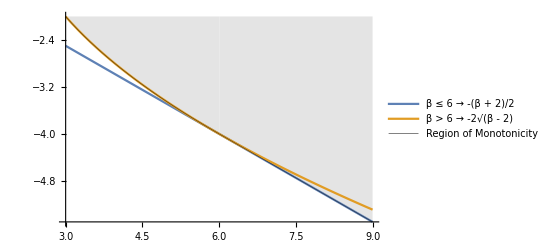

```mathematica
(* Plots of the lines representing conditions on β *)
Plot[{-(b+2)/2,-2 √(b-2),If[b≥6,-(b+2)/2,-2 √(b-2)]},{b,3,9},PlotLegends->{"β ≤ 6  →  -(β + 2)/2", "β > 6  →  -2√(β - 2)", "Region of Monotonicity"},Filling->{3->-2},FillingStyle->{3->LightGray},PlotStyle->{,,{Black,Thickness[.001],Opacity[.7]}}]
```

```mathematica
(* Construct a function for expanding out the monotonicity conditions to their final form (and algebraically simplifying). *)
isMonotone[DDX0_,DDX1_]:={
v=X1-X0;
h=(U1-U0)/2;
A0=DX0*2*h/v;
B0=DX1*2*h/v;
C0=DDX0*h*(h/v);
D0=DDX1*h*(h/v);
a=B0;
b=4*(B0-D0);
c=30-6*(2*(A0+B0)+C0-D0);
d=4*(A0+C0);
e=A0;
alpha=b*a^(-3/4)*e^(-1/4);
beta=c*a^(-1/2)*e^(-1/2);
gamma=d*a^(-1/4)*e^(-3/4);
alpha=Collect[Simplify[Expand[alpha]],{DDX0,DDX1}];
beta=Collect[Simplify[Expand[beta]],{DDX0,DDX1}];
gamma=Collect[Simplify[Expand[gamma]],{DDX0,DDX1}];
Print["α: ",alpha];
Print["β: ",beta];
Print["γ: ",gamma];
}[[1]];
isMonotone[DDX0,DDX1];
(*Print["\n-------------------------------------\n"]
Solve[alpha==(-(beta+2)/2)==gamma,{DDX0,DDX1}]*)
(*Print["\n-------------------------------------\n"]
Solve[alpha==(-2 √(beta-2))==gamma,{DDX0,DDX1}]*)
```

α: (4 ((DX1 (U0-U1))/(X0-X1))^(1/4))/((DX0 (U0-U1))/(X0-X1))^(1/4)+(DDX1 (U0-U1) ((DX1 (U0-U1))/(X0-X1))^(1/4))/(DX1 ((DX0 (U0-U1))/(X0-X1))^(1/4))

β: (3 DDX1 (-U0^2+2 U0 U1-U1^2))/(2 √((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)) (X0-X1))+(3 DDX0 (U0^2-2 U0 U1+U1^2))/(2 √((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)) (X0-X1))+(3 (-8 DX0 U0-8 DX1 U0+8 DX0 U1+8 DX1 U1+20 X0-20 X1))/(2 √((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)) (X0-X1))

γ: (4 DX0 ((DX1 (U0-U1))/(X0-X1))^(3/4))/(DX1 ((DX0 (U0-U1))/(X0-X1))^(3/4))+(DDX0 (-U0+U1) ((DX1 (U0-U1))/(X0-X1))^(3/4))/(DX1 ((DX0 (U0-U1))/(X0-X1))^(3/4))

```mathematica
(* Print the true and simplified expressions to verify that they are identical. *)
A=DX0*(U0-U1)/(X0-X1);
B=DX1*(U0-U1)/(X0-X1);

aFunc[DDX1_]:=DDX1*((U0-U1)*B^(1/4))/(DX1*A^(1/4))+(4*B^(1/4))/A^(1/4);
gFunc[DDX0_]:=DDX0*((U1-U0)*B^(3/4))/(DX1*A^(3/4))+(4*DX0*B^(3/4))/(DX1*A^(3/4));
bFunc[DDX0_,DDX1_]:=(DDX0-DDX1)*(3*(U0-U1)^2)/(2*(X0-X1)*A^(1/2)*B^(1/2))+(12*(DX0+DX1)*(U1-U0)+30*(X0-X1))/((X0-X1)*A^(1/2)*B^(1/2));
Print["α: ",aFunc[DDX1]];
Print["β: ",bFunc[DDX0,DDX1]];
Print["γ: ",gFunc[DDX0]];
Print["-----------------------------------------------------------------------------"]
Print["α: ",Collect[Simplify[Expand[aFunc[DDX1]]],{DDX0,DDX1}]];
Print["β: ",Collect[Simplify[Expand[bFunc[DDX0,DDX1]]],{DDX0,DDX1}]];
Print["γ: ",Collect[Simplify[Expand[gFunc[DDX0]]],{DDX0,DDX1}]];
```

α: (4 ((DX1 (U0-U1))/(X0-X1))^(1/4))/((DX0 (U0-U1))/(X0-X1))^(1/4)+(DDX1 (U0-U1) ((DX1 (U0-U1))/(X0-X1))^(1/4))/(DX1 ((DX0 (U0-U1))/(X0-X1))^(1/4))

β: (3 (DDX0-DDX1) (U0-U1)^2)/(2 √((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)) (X0-X1))+(12 (DX0+DX1) (-U0+U1)+30 (X0-X1))/(√((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)) (X0-X1))

γ: (4 DX0 ((DX1 (U0-U1))/(X0-X1))^(3/4))/(DX1 ((DX0 (U0-U1))/(X0-X1))^(3/4))+(DDX0 (-U0+U1) ((DX1 (U0-U1))/(X0-X1))^(3/4))/(DX1 ((DX0 (U0-U1))/(X0-X1))^(3/4))

-----------------------------------------------------------------------------

α: (4 ((DX1 (U0-U1))/(X0-X1))^(1/4))/((DX0 (U0-U1))/(X0-X1))^(1/4)+(DDX1 (U0-U1) ((DX1 (U0-U1))/(X0-X1))^(1/4))/(DX1 ((DX0 (U0-U1))/(X0-X1))^(1/4))

β: (3 DDX1 (-U0^2+2 U0 U1-U1^2))/(2 √((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)) (X0-X1))+(3 DDX0 (U0^2-2 U0 U1+U1^2))/(2 √((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)) (X0-X1))+(3 (-8 DX0 U0-8 DX1 U0+8 DX0 U1+8 DX1 U1+20 X0-20 X1))/(2 √((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)) (X0-X1))

γ: (4 DX0 ((DX1 (U0-U1))/(X0-X1))^(3/4))/(DX1 ((DX0 (U0-U1))/(X0-X1))^(3/4))+(DDX0 (-U0+U1) ((DX1 (U0-U1))/(X0-X1))^(3/4))/(DX1 ((DX0 (U0-U1))/(X0-X1))^(3/4))

```mathematica
(* Computation of Subscript[τ, 1] *)
tau1[A_,B_]:=24+2 √(A B)-3(A+B);
tau1[ρ A,ρ B]
Solve[tau1[ρ A,ρ B]==0,ρ]
```

24+2 √(A B ρ^2)-3 (A ρ+B ρ)

{{ρ→(24 (3 A-2 √A √B+3 B))/(9 A^2+14 A B+9 B^2)},{ρ→(24 (3 A+2 √A √B+3 B))/(9 A^2+14 A B+9 B^2)}}

-120/23+1728/(23 x)+1152/(23 √(x^2))

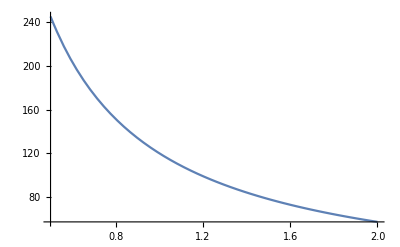

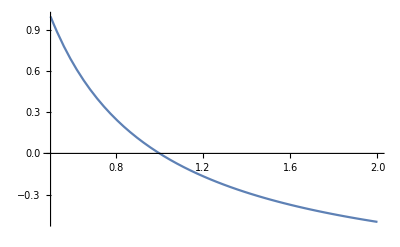

```mathematica
(* Plot the τ function to see why the algebraic solution works. *)
constant[ab_]:=24(3(ab)+2(ab^2)^(1/2))/(9*(ab^2)+14*(ab^2))
tau[ab_]:=24+2(ab^2)^(1/2)-3ab
tau[x]constant[x]//Simplify//Expand
Plot[constant[x]tau[x],{x,.5,2}]
Plot[1/x-1,{x,.5,2}]
```

```mathematica
(* Explicitly define the monotonicity conditions, look for simple solution expression. (FAILED) *)
v=X1-X0;
h=(U1-U0)/2;
A0=DX0*2*h/v;
B0=DX1*2*h/v;
C0=DDX0*h*(h/v);
D0=DDX1*h*(h/v);
a=B0;
b=4*(B0-D0);
c=30-6*(2*(A0+B0)+C0-D0);
d=4*(A0+C0);
e=A0;
alpha=b*a^(-3/4)*e^(-1/4);
beta=c*a^(-1/2)*e^(-1/2);
gamma=d*a^(-1/4)*e^(-3/4);
alpha=Collect[Simplify[Expand[alpha]],{DDX0,DDX1}];
beta=Collect[Simplify[Expand[beta]],{DDX0,DDX1}];
gamma=Collect[Simplify[Expand[gamma]],{DDX0,DDX1}];
(* Check to see what will happen to the monotonicity inequality as DX0 and DX1 are decreased (towards 0). *)
(*
U0=0;
U1=1;
X0=0;
X1=1;
DDX0=1;
DDX1=1;
DX0=DX1;
*)
(alpha-(-(beta+2)/2))//Expand
(alpha-(-2 √(beta-2)))//Expand
```

1+(4 X0 ((DX0 (U0-U1))/(X0-X1))^(3/4) ((DX1 (U0-U1))/(X0-X1))^(1/4))/(DX0 (U0-U1))+(DDX1 U0 X0 ((DX0 (U0-U1))/(X0-X1))^(3/4) ((DX1 (U0-U1))/(X0-X1))^(1/4))/(DX0 DX1 (U0-U1))-(DDX1 U1 X0 ((DX0 (U0-U1))/(X0-X1))^(3/4) ((DX1 (U0-U1))/(X0-X1))^(1/4))/(DX0 DX1 (U0-U1))-(6 U0 X0 √((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)))/(DX0 (U0-U1)^2)-(6 U0 X0 √((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)))/(DX1 (U0-U1)^2)+(3 DDX0 U0^2 X0 √((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)))/(4 DX0 DX1 (U0-U1)^2)-(3 DDX1 U0^2 X0 √((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)))/(4 DX0 DX1 (U0-U1)^2)+(6 U1 X0 √((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)))/(DX0 (U0-U1)^2)+(6 U1 X0 √((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)))/(DX1 (U0-U1)^2)-(3 DDX0 U0 U1 X0 √((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)))/(2 DX0 DX1 (U0-U1)^2)+(3 DDX1 U0 U1 X0 √((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)))/(2 DX0 DX1 (U0-U1)^2)+(3 DDX0 U1^2 X0 √((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)))/(4 DX0 DX1 (U0-U1)^2)-(3 DDX1 U1^2 X0 √((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)))/(4 DX0 DX1 (U0-U1)^2)+(15 X0^2 √((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)))/(DX0 DX1 (U0-U1)^2)-(4 ((DX0 (U0-U1))/(X0-X1))^(3/4) ((DX1 (U0-U1))/(X0-X1))^(1/4) X1)/(DX0 (U0-U1))-(DDX1 U0 ((DX0 (U0-U1))/(X0-X1))^(3/4) ((DX1 (U0-U1))/(X0-X1))^(1/4) X1)/(DX0 DX1 (U0-U1))+(DDX1 U1 ((DX0 (U0-U1))/(X0-X1))^(3/4) ((DX1 (U0-U1))/(X0-X1))^(1/4) X1)/(DX0 DX1 (U0-U1))+(6 U0 √((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)) X1)/(DX0 (U0-U1)^2)+(6 U0 √((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)) X1)/(DX1 (U0-U1)^2)-(3 DDX0 U0^2 √((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)) X1)/(4 DX0 DX1 (U0-U1)^2)+(3 DDX1 U0^2 √((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)) X1)/(4 DX0 DX1 (U0-U1)^2)-(6 U1 √((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)) X1)/(DX0 (U0-U1)^2)-(6 U1 √((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)) X1)/(DX1 (U0-U1)^2)+(3 DDX0 U0 U1 √((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)) X1)/(2 DX0 DX1 (U0-U1)^2)-(3 DDX1 U0 U1 √((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)) X1)/(2 DX0 DX1 (U0-U1)^2)-(3 DDX0 U1^2 √((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)) X1)/(4 DX0 DX1 (U0-U1)^2)+(3 DDX1 U1^2 √((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)) X1)/(4 DX0 DX1 (U0-U1)^2)-(30 X0 √((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)) X1)/(DX0 DX1 (U0-U1)^2)+(15 √((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)) X1^2)/(DX0 DX1 (U0-U1)^2)

2 √(-2+(3 DDX1 (-U0^2+2 U0 U1-U1^2))/(2 √((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)) (X0-X1))+(3 DDX0 (U0^2-2 U0 U1+U1^2))/(2 √((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)) (X0-X1))+(3 (-8 DX0 U0-8 DX1 U0+8 DX0 U1+8 DX1 U1+20 X0-20 X1))/(2 √((DX0 (U0-U1))/(X0-X1)) √((DX1 (U0-U1))/(X0-X1)) (X0-X1)))+(4 X0 ((DX0 (U0-U1))/(X0-X1))^(3/4) ((DX1 (U0-U1))/(X0-X1))^(1/4))/(DX0 (U0-U1))+(DDX1 U0 X0 ((DX0 (U0-U1))/(X0-X1))^(3/4) ((DX1 (U0-U1))/(X0-X1))^(1/4))/(DX0 DX1 (U0-U1))-(DDX1 U1 X0 ((DX0 (U0-U1))/(X0-X1))^(3/4) ((DX1 (U0-U1))/(X0-X1))^(1/4))/(DX0 DX1 (U0-U1))-(4 ((DX0 (U0-U1))/(X0-X1))^(3/4) ((DX1 (U0-U1))/(X0-X1))^(1/4) X1)/(DX0 (U0-U1))-(DDX1 U0 ((DX0 (U0-U1))/(X0-X1))^(3/4) ((DX1 (U0-U1))/(X0-X1))^(1/4) X1)/(DX0 DX1 (U0-U1))+(DDX1 U1 ((DX0 (U0-U1))/(X0-X1))^(3/4) ((DX1 (U0-U1))/(X0-X1))^(1/4) X1)/(DX0 DX1 (U0-U1))